## METEORA LIBRARY of BOOKS

```mathematica
bookSel = MeteoraBookSelect["Banham"]
```

{e_Banham__Critic_Writes,e_Banham__The_Architecture_of_the_Well_Tempered_Enviroment,e_Banham__Theory_and_Design_in_the_First_Machine_Age,e_Gannon__Reyner_Banham_and_the_Paradoxes_of_High_Tech,e_Whiteley__Reyner_Banham_Historian_of_the_Immediate_Future}

```mathematica
bookSel[[2]]
```

e_Banham__The_Architecture_of_the_Well_Tempered_Enviroment

```mathematica
$MeteoraWordData = 
 Uncompress@
  Import[CloudObject[
   "https://www.wolframcloud.com/obj/hovestadt/Published/METEORA DATASETS/MeteoraWordData"], "Text"];
```

```mathematica
"running"/.$MeteoraWordData["r","u", "n"]
```

{{Noun,Adjective},run}

```mathematica
MeteoraWordNounQ["tree"]
```

True

```mathematica
data=XenothekaTextImport@bookSel[[2]];
```

```mathematica
data=Import["https://raw.githubusercontent.com/amomorning/DB001212-code/main/books/Banham__The_Architecture_of_the_Well_Tempered_Enviroment.txt"];
```

```mathematica
data1 = StringReplace[data, {"\n" -> " ", "\"" -> "'"}];
```

```mathematica
data2 = ToLowerCase@data1;
```

```mathematica
words = TextWords@data2;
Length@words
```

66456

```mathematica
words1 = DeleteStopwords@words;
Length@words1
```

32265

```mathematica
nouns = Select[words1 , MeteoraWordNounQ];
Length@nouns
```

15837

```mathematica
stems  = MeteoraWordStem/@nouns;
Length@stems
```

15837

```mathematica
stems[[1;;20]]
```

{architectur,environ,univers,press,thought,buddi,sai,open,window,let,foul,air,open,window,let,foul,air,shout,book,grant}

```mathematica
dict = Sort@ DeleteDuplicates[stems];
Length@dict
```

2494

```mathematica
Select[dict, StringTake[#, 2]=="ab"&]
```

{abandon,aberr,abil,absenc,absolut,absolutist,absorpt,abstract,absurd,abund}

```mathematica
n5=Partition[stems,5,1]
```

Partition::pdep: Depth 1 requested in object with dimensions {}.

Partition[stems,5,1]

```mathematica
GetWordFriends[neighbours_, words_List] :=
  Module[{c},
      c = MeteoraWordStem@ToLowerCase@#;
      c -> Take[
             Reverse@SortBy[
                 Normal@Counts@
                   Flatten@Cases[
             neighbours, {a_, b_, c, d_, e_} -> {a, b, d, e}, 
                        All], Last], UpTo@6][[All, 1]]
      ] & /@ words
```

```mathematica
GetWordFriends[n5, {"rational"}]
```

{ration→{rigour,research,publish,practic,period,paint}}

```mathematica
GetWordFriends[n5, {"water"}]
```

{water→{air,vapour,steam,heat,us,temperatur}}

```mathematica
neighbours=n5;
```

```mathematica
c="water";
Take[ Reverse[SortBy[Normal@Counts@Flatten@Cases[neighbours, {a_, b_, c, d_, e_} -> {a, b, d, e}, All],Last]],UpTo[6]]
```

{air→12,vapour→5,steam→5,heat→5,us→4,temperatur→4}

```mathematica
word = "architecture";
n = 3;
wordCommunity = 
 Flatten@Cases[
   Rest@DeleteDuplicates@
     Flatten@NestList[
       GetWordFriends[n5, #[[-1, 2]]] &, {" " -> {word}}, 
       n], (a_String -> b_List) :> (DirectedEdge[a, #] & /@ b), All]
```

{architectur->modern,architectur->architectur,architectur->histori,architectur->glass,architectur->art,architectur->technolog,modern->architectur,modern->style,modern->opportun,modern->modern,modern->gener,modern->technolog,glass->light,glass->architectur,glass->wall,glass->heat,glass->us,glass->skin,art->light,art->architectur,art->year,art->technolog,art->electr,art->art}

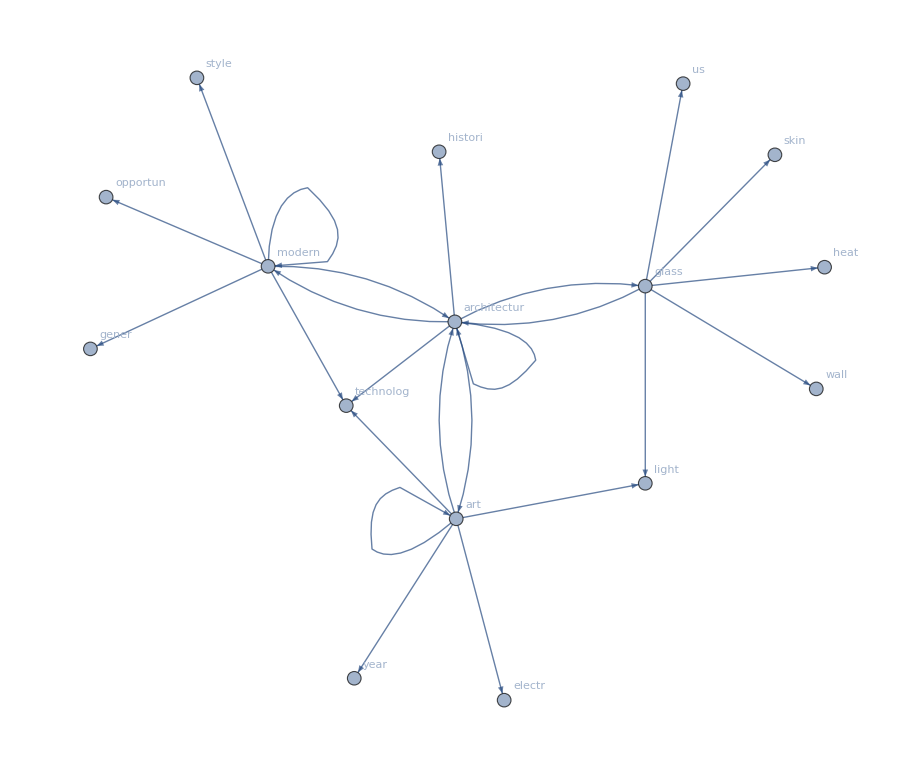

```mathematica
Graph[wordCommunity, VertexLabels -> "Name", GraphLayout -> "SpringEmbedding"]
```

```mathematica
MeteoraNGramConcepts[{"Verbrechen", "Kriminalität", "Computer"}, "German", {1800,  2018}, "normal"]
```

-Graphics-

```mathematica
MeteoraNGramConcepts[{"modernity", "Foucault"}, "English", {1800,  2018}, "normal"]
```

-Graphics-

```mathematica
paragraphs = StringSplit[data, "\n"]
```

{Reyner Banham,937,Willis Carrier, Father of Air Conditioning, by Margaret Ingels, Garden City, 1952, which contains an invaluable tabulated ch…d developments in ventilation and refrigeration from the Renaissance to 1950, to which the present study is deeply indebted.}
 |  |  |  |

```mathematica
StringSplit[data, "\n"]//Dimensions
```

{939}

```mathematica
paragraphs = MapIndexed[{"banham", First@#2} -> #1 &, paragraphs];
Length@paragraphs
```

939

```mathematica
paragraphs1 = MeteoraParagraphsBrokenJoin[paragraphs];
Length@paragraphs1
```

429

```mathematica
paragraphs1[[100]]
```

{banham,214}→This was an enormous step forward, especially when the neat and convenient inverted mantle was introduced, and everyone who has lived with domestic lighting by gas will know that it has much to recommend it—a warm, murmuring, friendly radiance, of quite a pleasant colour-spectrum when correctly trimmed. The gas mantle, together with its heating partner, the incandescent gas fire (models using asbestos string as the radiants were available from the early 1880’s) might have had a great future, but for two things. The first was von Welsbach’s attitude as primary patent holder, combining as it did an almost feudal conception of absolute property rights, a Levantine deviousness in financial methods, and a straightforward nineteenth-century determination to make as big a killing as possible, which all combined to leave him trying to hold the market to ransom at the very moment when deliverance was at hand in the shape of the second thing—the perfection of a workable system of domestic electric lighting. The Welsbach mantle appeared on the scene just too late to establish itself fully before the whole basis of gas illumination was swept away by the triumph of Edison and Swan.

```mathematica
paragraphs[[214]]
```

{banham,214}→This was an enormous step forward, especially when the neat and convenient inverted mantle was introduced, and everyone who has lived with domestic lighting by gas will know that it has much to recommend it—a warm, murmuring, friendly radiance, of quite a pleasant colour-spectrum when correctly trimmed. The gas mantle, together with its heating partner, the incandescent gas fire (models using asbestos string as the radiants were available from the early 1880’s) might have had a great future, but for two things. The first was von Welsbach’s attitude as primary patent holder, combining as it did an almost feudal conception of absolute property rights, a Levantine deviousness in financial methods, and a straightforward nineteenth-century determination to make as big a killing as possible, which all combined to leave him trying to hold the market to ransom at the very moment when deliverance was at hand in the shape of the second thing—the perfection of a workable system of domestic electric lighting. The Welsbach mantle appeared on the scene just too late to establish itself fully before the whole basis of gas illumination was swept away by the triumph of Edison and Swan.

```mathematica
sentences = 
  Flatten@Cases[
    paragraphs1[[1 ;; -1]], (_List -> a_String) :> 
     Select[TextSentences@a, StringLength[#] > 60 &], All];
Length@sentences
```

1636

```mathematica
sentences[[100]]
```

Thick and weighty structures are less easily overthrown by storm or earthquake, less maimed by fire or flood.

{{banham,1}→Reyner BanhamThe architecture of the well-tempered environmentThe University of Chicago PressI thought I heard Buddy Bolden say.,427,{banham,938}→And, finally, a work intended for a general read…, to which the present study is deeply indebted.}
 |  |  |  |

Some architects, like the Adam brothers, made ingenious use of ‘left spaces’ in plan to provide concealed access for servants to light lamps and candles.

```mathematica
Intersection[Select[TextSentences[data1],StringLength[#]>60&],sentences]//Length
```

1235

```mathematica
stringToFind = "water";
```

```mathematica
selection = 
 Flatten[Position[sentences, #] & /@ 
   Select[sentences, 
    StringContainsQ[ToLowerCase@#, ToLowerCase@stringToFind] &]]
```

{7,76,95,96,109,122,173,191,193,217,222,228,238,249,260,279,280,281,284,297,343,396,401,514,519,520,522,540,610,612,647,651,669,682,687,692,700,717,807,835,1035,1037,1038,1040,1041,1043,1045,1046,1047,1073,1093,1486,1502,1580,1633}

```mathematica
CellPrint /@
  (Cell[
      TextData[
       MeteoraTextHighlightParagraphs[sentences[[#]], {stringToFind}]], 
      "Text"] & /@ selection);
```

The fact that the outpourings of a radio may be understood as information or environmental background, that the flow of hot water through a pipe may be seen as contributing to the maintenance of an environmental condition or the transmission of a useful product, should warn us that the making of even the division proposed above is open to serious questioning, though the validity of this division for the purposes of the present book, which discusses the architecture of environment, should emerge as the argument proceeds.

Against this, societies who do not build substantial structures tend to group their activities around some central focus—a water hole, a shade tree, a fire, a great teacher—and inhabit a space whose external boundaries are vague, adjustable according to functional need, and rarely regular.

Fires have had to be burned in winter, lamps lit in the evening, muscle power for fans, water power for fountains used in the heat of the day.

The design of buildings has always had to make some provision in plan and section, for these marginal consumptions of environmental power—chimneys for smoke, channels for water.

But if these various modes should not be too sharply distinguished in traditional practice, there is an important geographical or climatic consideration that distinguishes solutions that are more conservative from those thatare more selective, and an historical watershed that separates both of these from solutions that are primarily regenerative.

While the deficient humidity of an overdried climate can be crudely made good by splashing water about and using shade to reduce evaporative loss, the removal of excess water from the atmosphere has so effectively defied all pre-technological efforts, that it has usually made better sense for those who could afford it to move elsewhere—the British in India retiring to hill-stations like Simla, New York business men with lung complaints to Colorado.

Crossing the Chicago River and seeing hot water and steam from the sewer pipes of individual buildings emptying into the river, and when walking along the streets and seeing steam escaping from manholes, fixed in mind ‘Wastefulness’ and suggested the thought; ‘What does the needless waste from these sources cost Chicago daily—§50,000-5100,000 P’1Not only this, but there was obviously a matching wastefulness of human resources.

We may as well supply a house with water by making a trap-door in the roof to admit rain.

In the effective absence, from most buildings, of any system of ducted and force-fed ventilation (comparable with piped water under a sufficient head of pressure to make it go where it was needed) the movement of air was an almost uncontrollable function of the entire building structure, complete with its ancillary services and external weather conditions—the shade of a single tree, the closing of a door or the lighting of a fire in a spare bedroom might make the difference between tolerable and intolerable conditions.

The second consists of the family bed-rooms with breakfast room . . . and the third floor of the servants’ bed-rooms with children’s play-room, store room and two water-cistern rooms.

Along beneath the ceiling of the basement of this corridor run five coils of Perkins’ one-inch diameter hot water pipes.

The flue from each room opens separately into this chamber, and there is also a flue from the cloak room, the dressing room, the bath room, and the kitchen, and from all the water-closets, even the servants’ in the basement; there are eighteen flues . . .

The aims and priorities of heating are set out in crisp phrases of crushingly mechanistic insensitivity, thus:BOILER: in warming by steam or water, the boiler is generally the first consideration.10It is usual to maintain a temperature of 70°F within a room.11It may be asked ‘Why is the question of condensation the first consideration?’ and in reply I will say that it furnishes us with the first item of data on which to base all our other calculations . . .12It may be objected that Baldwin can treat matters thus because there was a going consensus of opinion that rooms should be kept at 70°F and that no further human study was needed at the time.

Attempts to do away with the draught could be as complex as Dr Hayward’s, or as self-frustrating as a case recorded by Baldwin:In well-built modern residences the construction is often so good that it will hold water ... a grand New York residence was so air-tight that the air to supply the grate fires had to come down the register flues (and) the air had to come down the ventilating flue of the hood of the range in order to supply the range fire, until a window was opened.14 14 ibid., p 53.

On the other hand, substances and impurities that cannot be estimated from the presence of carbonic acid, as for instance an excessive amount of vapour of water, sickly odours from respiratory organs, unclean teeth, perspiration, untidy clothing, the presence of microbes due to various conditions, stuffy air from dusty carpets and draperies, and many other factors that may combine, will in most cases cause greater discomfort and greater ill-health.16What is striking about Meier’s demonology of bad air is that it not only includes the real culprits, carbon dioxide (carbonic acid gas) and water vapour, but still retains nearly all the common Victorian villains, such as ‘sickly odours’ and makes provision forany demons he may have overlooked (‘many other factors’).

In the absence of machinery of domestic scale most of this power had, of need, to be applied directly and crudely to the immediate environment, since water was the only substance commonly channelled through pipes or conduits.

However, the fact that water could be heated, and then circulated through pipes, afforded the prototype of most later forms of sophisticated environmental control—the combustion of the fuel at one convenient point, and the application of the energy thus generated at some other convenient or necessary point.

The first proposals to use hot water in this way go back into the Renaissance, but their practical application belongs to the pioneer phases of steam technology in the late eighteenth century—James Watt had his own office heated by steam in 1784, and legend has it that the earliest building heated from the first by such methods was Matthew Murray’s ‘ Steam Hall’ in Leeds in the first years of the nineteenth century.

By the 1860’s, heating by steam or hot water could be looked for in most buildings, public or domestic, of any pretensions; considerable skill had accumulated in the design of the installations, both on paper and at the level of field decisions that had to be made by foremen and pipe-fitters.

However much the innumerable patented ‘improvements’ to stoves in the nineteenth century might have boosted their performance by better combustion or transference of heat to the ambient air, however much the design of steam and hot water radiators may have become sophisticated, the stove, grate or radiator stood at some point in the room dictated by custom, convenience or aesthetic preference and the warming of the space around it was at the mercy of draughts, open windows, local convection from lamps, obstruction due to furniture, etc.

But, given the much greater heat load of flame light sources, and the atmospheric load of water-vapour, carbon oxides and pure carbon which they also generated, there would seem to have been little point in Carrier and Cramer even starting on air-conditioning until the filament electric lamp had abolished most of this atmospheric garbage at a single blow.

To achieve it, many detailed triumphs and felicities of technological ingenuity were required, sometimes combined with gratifying civic foresight, as when Edison, observing. . . you don’t lift waterpipes and gas-pipes up on stilts.12insisted on saddling himself with the task of inventing satisfactory and properly insulated underground conductors for his power, instead of imitating the overhead cables of telephone practice, which used the surrounding air as a cheap insulator.

He seems to have known, on the basis ofthis experience, that although an electrical distribution network could not have the storage capacity that enables a gas or water network to cope instantly with a tap turned on or off, there were still margins enough of tolerance in a complex electrical system for suitable equipment and control techniques to handle what was theoretically beyond control, and thus to achieve an effective subdivision of the electric light.

Air, on entering through window-type openings in the ends of the engine-house, was pulled through hanging curtains of coconut fibre robes kept moist by sprinklers in the roof of the filter-chamber (this water could be warmed in winter to prevent freezing).

But the winter was also the time when there was the biggest difference in external and internal air temperatures—air entering the system below freezing would leave it at a temperature in the sixties Fahrenheit—and thus the greatest reduction in relative humidity, in any system that did not make good the deficiency in the water-vapour content of the air.

But this deficiency was, crudely, made good by the sprinkler system, more or less in direct ratio to need, because the colder the day, the more soot would be pumped into the Belfast atmosphere, and the more water would be run through the sprinklers and taken up by the air that passed through the ropes.

From the beginning, Davidson had intended some form of humidity control, and before 1920, if medical memories are to be trusted, it became the practice to observe the humidity of the air in the wards night and morning, by the normal wet-bulb/dry-bulb thermometer technique, and instruct the engineman to regulate the flow of water over the filter ropes accordingly.

Furthermore, the abandonment of the Plenum system (due to insufficient upkeep rather than inherent faults in the design) and its substitution by an extended hot-water radiator system has done much to destroy the spatial artistry for which Mackintosh is renowned and of which the school is reckoned his masterpiece.

All this is meant to be achieved by a single heated flue and extract, around which the equipment clusters, sending out good air and hot water, and into which foul air is recalled and disposed of.

It carries no fireplaces or chimneys, no water-piping of any consequences, nor—since one may safely posit a lightweight, balloon-frame construction by this date—does it act as much of a thermal barrier.

Thus:Another modern opportunity is afforded by our effective system of hot-water heating.

Although the statement begins with hot-water heating, it proceeds directly to the improvement of aspect and ventilation made possible by articulating the house into more separate parts, and in the process it inevitably involves lightweight construction on two counts.

The hearth is little more than a visual effect, a sentimental symbol of home—the room is adequately heated, even in the depth of winter, by a hot water system of pipes running around the perimeter of the room concealed in the wainscoting, to serve a massive radiator under the window-seat, which is slatted to permit the warmed air to circulate.

But the second, linked lesson, is that this rich and iimproved environmental performance* was achieved without recourse to any technological novelties—though Wright refers to hot water heating as a modern opportunity, it is the manner of seizing the opportunity that is modern, not the manner of heating, which Was already a century or more old, and the manner of seizing the opportunity clearly has a great deal to do with the working together of the parts of the building.

Peter Behrens’s house for his own occupation in Darmstadt was built in the same year, has about the same usable floor-area, has a comparable heating technology (hot water pipes under window-seats) and its architect was almost exactly the same age as Wright and about the same fame in the land.

Compared to this, the Behrens house, in spite of its electric lighting and hot-water heating, is like a survivor from an earlier civilisation, the civilisation that had produced Catherine Beecher’s Neo-Grec box of 1842, but not the American Woman’s Home of 1869.

Within these curious cupboards are hot-water radiators placed edge-on to the room and concealed by slatted wooden grilles.

There is room enough for them, and there is a massive hot water pipe in the bottom of the cavity provided for them, but they are not there now.

The stand that Scheerbart adopts looks startling at a time when almost everybody, and not just the electrical industry, seemed bent upon greater and greater levels of illumination, but later events, and the research methods developed for scientific lighting studies seem to justify almost every word of arguments like these:When we haye light in plenty, as the fuller exploitation of wind and waterpower will make possible, so we will have less need to leave the light clear, and will be able to temper it with colours . . .1:lFull white light is the cause of at least part of the neurosis of our time.

In the Employment Exchange for the city of Dessau, for instance, the hot-water radiators on the edge of the floor-slab at each landing of the main staircase serve not only to temper the chill of a multi-storey window forming the whole of one wall of the stair-well, but also double as balustrades to prevent persons walking through the glass.

According to Carrier’s own account, recalled in old age, his response to air so laden with water droplets as to impede the sight, was:Here is air approximately 100% saturated with moisture.

Now, if I can saturate the air and control the temperature at saturation, I can get air with any amount of moisture I want in it.2Such an observation cannot have failed to occur to others beside Carrier, once the mechanics of atmospheric humidity were understood, but by phrasing the matter in this way, he would almost automatically suggest a mechanism whereby that moisture could be controlled—to govern the absolute water vapour content of abody of air by holding it, in the presence of excess water, at the temperature at which the maximum of water vapour it could be made to hold was the same as the amount desired, and then to remove the excess water droplets and restore the air to the temperature at which it was required to be circulated.

This, obviously, meant regulating the temperature of the air twice, once to achieve the correct dew-point conditions required to-regulate the total water-content, and then once more, to restore (usually to a higher temperature) the correct thermal content for circulation.

His account of the Pittsburgh vision continues:I can do it, too (soil., ‘get air with any amount of moisture I want.’), by drawing the air through a fine spray of water to create actual fog.

By controlling the water temperature I can control the temperature at saturation.

The cold-water spray will actually be the condensing surface.

Water won’t rust.3A knowledge of normal high-school physics will confirm the propriety of Carrier’s method, but common-sense still boggles at the realisation that, for most of the air-conditioning year in most of the climates where air-conditioning is necessary.

Carrier was proposing to dry air by pumping it full of water—and this, not as a bench-top trick at a Christmas demonstration lecture, but as a commercial proposition, twenty-four hours a day.

It did not become practical at once, however; some years of trial and error with types and dispositions of spray-nozzles, and with baffle-systems to remove unwanted air-borne droplets of water from the saturated air were required.

Air is admitted to a basement chamber, into which, in summer, sprays of water are introduced; it is then driven over the steam piping and on into a mixing chamber . . .

Carrier’s solution—and ultimately everybody else’s—was to distribute filtered and moisture-controlled air at high velocity through small diameter ducts, and heat it or cool it at the point of delivery under the windows of the offices by means of pipe-coils warmed or chilled by water supplied on a separate network.

But they are not the consummation, merely one of a range of consummations, for thereare stepped hydroplanes as beautiful in shape, hydrofoils as compelling in motion, cushion craft handier and safer in shoal waters, and a whole range of sub-aqua vehicles that can go where a yacht cannot, and would be helpless if it could.

The difference of means is this: at Versailles the enclosure of space by massive structure is paramount, and the idiom thus created sets the cues for the manipulation of space by other means, such as planting and water; whereas at Las Vegas, structure is the least dominant element in the definition of symbolic space.

But about its thermal environment there seems to be no surviving doubt, now that its emergency hot-water heating system has been removed, unused, after the school had survived almost the worst winter in living memory (1962-3).

For those who simply wish to reinforce their understanding with background reading, the situation is less fortunate, because of the dearth of general works on the subject, about which complaint is made in chapter i. However, the following works may prove helpful:A Short History of Technology, by Derry and Williams, Oxford, i960; especially chapters 14, 17 and 22, which give some account of water-supply, drainage, coal gas and electricity.

```mathematica
CellPrint@ (Cell[ TextData[ MeteoraTextHighlightParagraphs[sentences[[7]], {stringToFind}]],"Text"]);
```

The fact that the outpourings of a radio may be understood as information or environmental background, that the flow of hot water through a pipe may be seen as contributing to the maintenance of an environmental condition or the transmission of a useful product, should warn us that the making of even the division proposed above is open to serious questioning, though the validity of this division for the purposes of the present book, which discusses the architecture of environment, should emerge as the argument proceeds.

```mathematica
Cell[ TextData[
       MeteoraTextHighlightParagraphs[sentences[[7]], {stringToFind}]], 
      "Text"] //CellPrint
```

The fact that the outpourings of a radio may be understood as information or environmental background, that the flow of hot water through a pipe may be seen as contributing to the maintenance of an environmental condition or the transmission of a useful product, should warn us that the making of even the division proposed above is open to serious questioning, though the validity of this division for the purposes of the present book, which discusses the architecture of environment, should emerge as the argument proceeds.

```mathematica
paragraphs2 = Flatten[MeteoraParagraphTooLargeSplit /@ paragraphs1];
Length@paragraphs2
```

781

```mathematica
paragraphs3 = Select[paragraphs2, StringLength@#[[2]] > 100 &];
Length@paragraphs3
```

756

```mathematica
Head@paragraphs3[[1]]
```

Rule

```mathematica
fe = FeatureExtraction[
  paragraphs3[[All, 2]], {"LowerCasedText", "WordVectors"}]
```

FeatureExtractorFunction[…]

```mathematica
fe@"hello there"
```

{{-0.38497,0.80092,0.064106,-0.28355,-0.026759,-0.34532,-0.64253,-0.11729,-0.33257,0.55243,-0.087813,0.9035,0.47102,0.56657,0.6985,-0.35229,-0.86542,0.90573,0.03576,-0.071705,-0.12327,0.54923,0.47005,0.35572,1.2611,-0.67581,-0.94983,0.68666,0.3871,-1.3492,0.63512,0.46416,-0.48814,0.83827,-0.9246,-0.33722,0.53741,-1.0616,-0.081403,-0.67111,0.30923,-0.3923,-0.55002,-0.68827,0.58049,-0.11626,0.013139,-0.57654,0.048833,0.67204},{0.68491,0.32385,-0.11592,-0.35925,0.49889,0.042541,-0.40153,-0.36793,-0.61441,-0.41148,-0.3482,-0.21952,-0.22393,-0.64966,0.85443,0.33582,0.2931,0.16552,-0.55082,-0.61277,-0.14768,0.47551,0.65877,-0.07103,0.56147,-1.2651,-0.74117,0.36365,0.5623,-0.27365,3.8506,0.27645,-0.1009,-0.71568,0.18511,-0.12312,0.56631,-0.22377,-0.016831,0.57539,-0.51761,0.033823,0.19643,0.63498,-0.24866,0.038716,-0.50559,0.17874,-0.1693,0.062375}}

```mathematica
Rule["a",1]
```

a→1

```mathematica
fe[paragraphs3[[1,2]]];
```

```mathematica
dr = DimensionReduction[Normal@fe@paragraphs3[[All, 2]], 30]
```

DimensionReducerFunction[…]

```mathematica
pv = MapIndexed[#1 -> First@#2 &, dr /@ fe@paragraphs3[[All, 2]]];
```

```mathematica
AskMyBook[txt_] := 
 CellPrint@ 
    Cell[#[[1, 1]] <> " " <> ToString@#[[1, 2]] <> ": " <> #[[2]], 
     "Text"] & /@ paragraphs3[[Nearest[pv, dr@fe@txt, 3]]]
```

```mathematica
AskMyBook[
  "What is the law of the probabilities of errors of which the elements are still susceptible that we draw from them ? This is made clear to u$ by the theory of probabilities. "]
```

banham 886:  This combination of circumstance is fortunate for the- shelter industry, since it means that, over time, the spread of tolerances is effectively wider than totally and minutely quantifiable laboratory tests might suggest. Given variation in time, the human body adapts itself to short term changes; the environmental control system does not have to make instant adaptation to every degree ofanticipate the effects of boiling a kettle or opening the fridge door. In many strictly lethal circumstances the time taken to get up from a chair, walk to a window and open it, is not a life and death consideration, and for less acute situations of vitiation or risk it may not be fatal to wait for someone else to become aware of the problem and open the window for you.

banham 34:  It has seemed better, in many cases, to settle for a building which appears to sum up forward thinking and progressive practice and let it stand as typical of the best or most interesting work being done at the time, but not to attribute to the concept of typicality those overtones of a platonic absolute implicit (and explicit) in Giedion’s elevation of Linus Yale to the status of the very type of the Yankee inventor. The use of typicality in the chapters that follow is purely illustrative, the buildings singled out for mention tend less to be the first of their class, than ‘ among the first.’

banham 144:  For Baldwin, it appears that questions of human comfort and physiological response to thermal stimuli either do not exist, or are not open to discussion. The aims and priorities of heating are set out in crisp phrases of crushingly mechanistic insensitivity, thus:BOILER: in warming by steam or water, the boiler is generally the first consideration.10It is usual to maintain a temperature of 70°F within a room.11It may be asked ‘Why is the question of condensation the first consideration?’ and in reply I will say that it furnishes us with the first item of data on which to base all our other calculations . . .12It may be objected that Baldwin can treat matters thus because there was a going consensus of opinion that rooms should be kept at 70°F and that no further human study was needed at the time.

{Null,Null,Null}